```mathematica
Problem 1
Consider the function f(𝑥)=(1+𝑥)𝑥.
a.Estimate the value of lim(1+𝑥)𝑥 by constructing a table similar to those given in 𝑥->0
Section 2.2.Is this value familiar?
b.Graph 𝑓(𝑥).Does the graph confirm your idea from part a?

Part A
```

```mathematica
f[x_]=(1+x)^(1/x)
```

(1+x)^(1/x)

```mathematica
f[{5,3,1,.5,.25,.1,.01,.001,-.001,-.01,-.1,-.25,-.5,-1,-3,-5}]
```

Power::infy: Infinite expression 1/0 encountered.

{6^(1/5),2^(2/3),2,2.25,2.44141,2.59374,2.70481,2.71692,2.71964,2.732,2.86797,3.16049,4.,ComplexInfinity,-(-1)^(2/3)/2^(1/3),-(-1)^(4/5)/2^(2/5)}

```mathematica
%//TableForm
```

6^(1/5)
2^(2/3)
2
2.25
2.44141
2.59374
2.70481
2.71692
2.71964
2.732
2.86797
3.16049
4.
ComplexInfinity
-(-1)^(2/3)/2^(1/3)
-(-1)^(4/5)/2^(2/5)

```mathematica
The table is approching 2.75


Part B
```

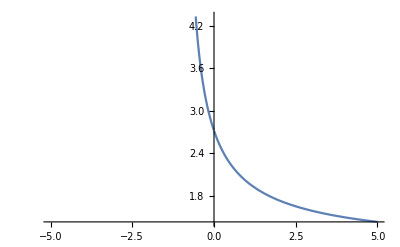

```mathematica
p1=Plot[f[x],{x,-5,5}]
```

```mathematica
The graph is also approching 2.75,it confirms the result of part A
```

```mathematica
ClearAll
```

ClearAll

```mathematica
Problem 2
Use the Squeeze Theorem to show that lim √𝑥3+𝑥2 sin (𝜋)=0. Illustrate by graphing the appropriate 𝑓,𝑔,h functions on the same plot.
```

```mathematica
f[x_]=((x^3+x^2)^(1/2))(Sin[Pi/x])
```

√(x^2+x^3) Sin[π/x]

```mathematica
g[x_]=-(x^3+x^2)^(1/2)
```

-√(x^2+x^3)

```mathematica
h[x_]=(x^3+x^2)^(1/2)
```

√(x^2+x^3)

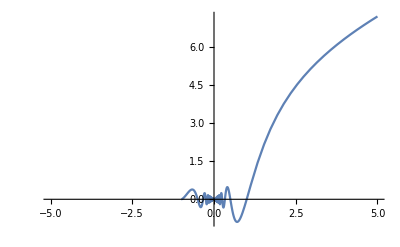

```mathematica
p1=Plot[f[x],{x,-5,5}]
```

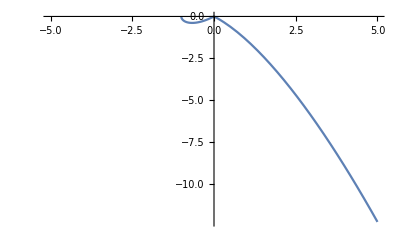

```mathematica
p2=Plot[g[x],{x,-5,5}]
```

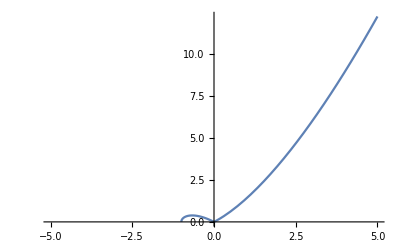

```mathematica
p3=Plot[h[x],{x,-5,5}]
```

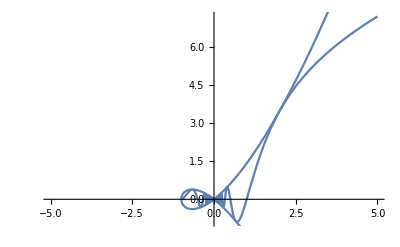

```mathematica
Show[p1,p2,p3]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
Problem 3
Use the Intermediate Value Theorem to show that the equation arctan 𝑥=1−𝑥 has at least one solution.Use Mathematica to approximate one solution.

ArcTan[x]=1-x
0=ArcTan[x]+x-1
```

```mathematica
f[x_]=ArcTan[x]+x-1
```

-1+x+ArcTan[x]

```mathematica
f[0]
```

-1

```mathematica
f[1]
```

π/4

```mathematica
therefore, there must be a f(x) that equals 0
```

```mathematica
m=(Pi/4+1)/(1-0)
```

1+π/4

```mathematica
f'[x]
```

1+1/(1+x^2)

```mathematica
Solve[1+π/4==1+1/(1+x^2)]
```

{{x→-√((4-π)/π)},{x→√((4-π)/π)}}

```mathematica
N[{{x->-√((4-π)/π)},{x->√((4-π)/π)}}]
```

{{x→-0.522723},{x→0.522723}}

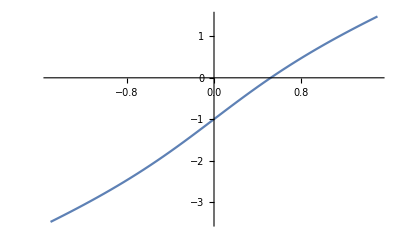

```mathematica
p1=Plot[f[x],{x,-1.5,1.5}]
```

```mathematica
c=.52
```

```mathematica
ClearAll
```

ClearAll

```mathematica
Problem 4

The curve 𝑦=𝑥 is called a serpentine.Find the equation of the tangent line to the 1+𝑥2
curve at the point (3,0.3).Graph the curve and the tangent line together on the same plot.
```

```mathematica
f[x_]=x/(1+x^2)
```

x/(1+x^2)

```mathematica
f'[x]
```

-(2 x^2)/((1+x^2)^2)+1/(1+x^2)

Solve::naqs: -(2 x^2)/((1+x^2)^2)+1/(1+x^2) is not a quantified system of equations and inequalities.

```mathematica
Simplify[-(2 x^2)/((1+x^2)^2)+1/(1+x^2)]
```

(1-x^2)/((1+x^2)^2)

```mathematica
g[x_]=(1-x^2)/((1+x^2)^2)
```

(1-x^2)/((1+x^2)^2)

```mathematica
g[3]
```

-2/25

```mathematica
Solve[0.3==-2/25(3)+b]
```

{{b→0.54}}

```mathematica
So
```

```mathematica
h[x_]=-2/25 x+.54
```

0.54-(2 x)/25

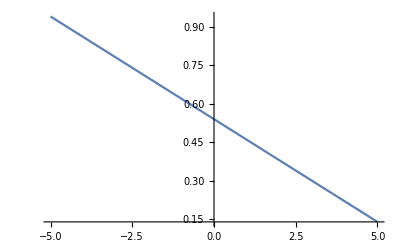

```mathematica
p1=Plot[h[x],{x,-5,5}]
```

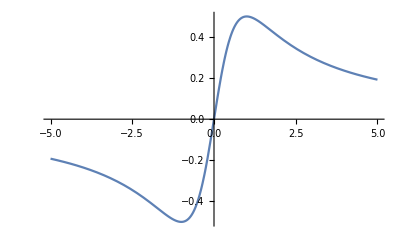

```mathematica
p2=Plot[f[x],{x,-5,5}]
```

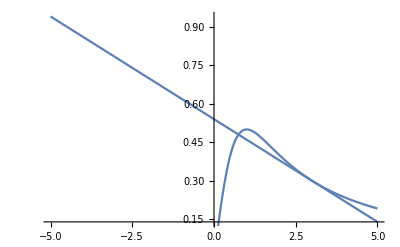

```mathematica
Show[p1,p2]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
Problem 5
Find the following derivatives:
a.𝑑803[cos 𝑥] 𝑑𝑥803
b.𝑑34[sin(2𝑥)]

Part A
```

```mathematica
f[x_]=Cos[x]
```

Cos[x]

```mathematica
D[f[x],{x,803}]
```

Sin[x]

```mathematica
Part B
```

```mathematica
g[x_]=Sin[2x]
```

Sin[2 x]

```mathematica
D[g[x],{x,34}]
```

-17179869184 Sin[2 x]

```mathematica
ClearAll
```

ClearAll

```mathematica
Problem 6
Consider the curve 𝑥2𝑦2=(𝑦+1)2(4−𝑦2).Find the equation of the tangent line to the curve at the point (2√3,1).
```

```mathematica
Dt[x^2y^2==(y+1)^2(4-y^2),x]
```

2 x y^2+2 x^2 y Dt[y,x]==-2 y (1+y)^2 Dt[y,x]+2 (1+y) (4-y^2) Dt[y,x]

```mathematica
Simplify[%,Dt[y,x]]
```

-(x y^2)/(-4+(-3+x^2) y+3 y^2+2 y^3)

```mathematica
j[x_,y_]=-(x(y)^2)/(-4-3y+x^2y+3y^2+2y^3)
```

-(x y^2)/(-4-3 y+x^2 y+3 y^2+2 y^3)

```mathematica
m=j[2√3,1]
```

-(√3)/5

```mathematica
Solve[1==(-√3)/5(2√3)+b]
```

{{b→11/5}}

```mathematica
So the equatiopn of the tangent line at (2√3,1) is

y=(-√3)/5 x+11/5
```

```mathematica
ClearAll
```

ClearAll

```mathematica
Problem 7
Consider the equation of motion 𝑠(𝑡)=𝑡2𝑒−𝑡 where 𝑠 is measured in feet and 𝑡≥0 is measured in seconds.
a.Find the velocity and acceleration functions
         b.Graph position,velocity,and acceleration on the same plot.
    c.Find the intervals of speeding up and slowing down.


Part A
```

```mathematica
s[t_]=(t^2)(E^(-t))
```

ⅇ^-t t^2

```mathematica
t>0
```

t>0

```mathematica
s'[t]
```

2 ⅇ^-t t-ⅇ^-t t^2

```mathematica
v[t_]=2E^(-t)-E^(-t)t^2
```

2 ⅇ^-t-ⅇ^-t t^2

```mathematica
s''[t]
```

2 ⅇ^-t-4 ⅇ^-t t+ⅇ^-t t^2

```mathematica
a[t_]=2E^(-t)-4E^(-t)(t)+E^(-t)(t^2)
```

2 ⅇ^-t-4 ⅇ^-t t+ⅇ^-t t^2

```mathematica
Part B
```

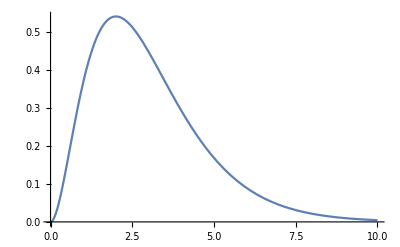

```mathematica
p1=Plot[s[t],{t,0,10}]
```

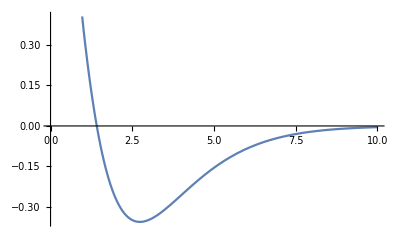

```mathematica
p2=Plot[v[t],{t,0,10}]
```

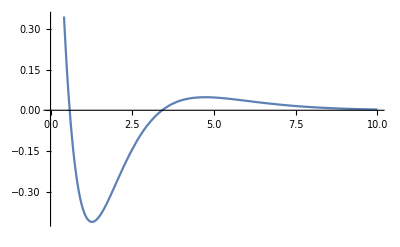

```mathematica
p3=Plot[a[t],{t,0,10}]
```

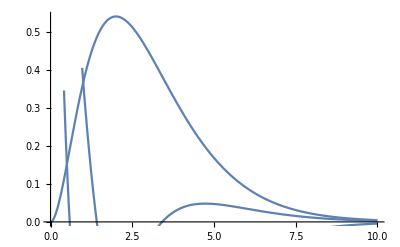

```mathematica
Show[p1,p2,p3]
```

```mathematica
Part C
```

```mathematica
Solve[0==2E^(-t)-4E^(-t)(t)+E^(-t)(t^2)]
```

{{t→2-√2},{t→2+√2}}

```mathematica
a[.5]
```

0.151633

```mathematica
a[2]
```

-2/ⅇ^2

```mathematica
a[3.5]
```

0.00754935

```mathematica
Speeding Up on Interval (0,2-√2)in union with (2+√2,Infinity)
Slowing Down on Interval (2-√2,2+√2)
```

```mathematica
ClearAll
```

ClearAll

```mathematica
Problem 8
Find the linearization 𝐿(𝑥) for the function 𝑓(𝑥)=2 sin 2𝑥 at 𝑎=𝜋8.Use it approximate 𝐿 (25).How does it compare to 𝑓 (25)?
```

```mathematica
f[x_]=2Sin[2x]
```

2 Sin[2 x]

```mathematica
f'[x]
```

4 Cos[2 x]

```mathematica
f'[Pi/8]
```

2 √2

```mathematica
f[Pi/8]
```

√2

```mathematica
Solve[√2==2√2(Pi/8)+b]
```

{{b→1/4 (4 √2-√2 π)}}

```mathematica
L[x_]=2√2(x)+1/4 (4 √2-√2 π)
```

1/4 (4 √2-√2 π)+2 √2 x

```mathematica
f[2/5]
```

2 Sin[4/5]

```mathematica
N[2 Sin[4/5]]
```

1.43471

```mathematica
L[2/5]
```

(4 √2)/5+1/4 (4 √2-√2 π)

```mathematica
π Rationalize[N[(4 √2)/5+1/4 (4 √2-√2 π)]/π]
```

1.43486

```mathematica
L(2/5) and f(2/5) are very similar.
```

```mathematica
ClearAll
```

ClearAll

```mathematica
Problem 9
Find the critical numbers for 𝑓(𝑥)=𝑥3(4−𝑥)3.
```

```mathematica
f[x_]=x^(1/3)(4-x)^(2/3)
```

(4-x)^(2/3) x^(1/3)

```mathematica
f'[x]
```

(4-x)^(2/3)/(3 x^(2/3))-(2 x^(1/3))/(3 (4-x)^(1/3))

```mathematica
Solve[0==(4-x)^(2/3)/(3 x^(2/3))-(2 x^(1/3))/(3 (4-x)^(1/3))]
```

{{x→4/3}}

```mathematica
The Critical numbers for f(x) are 0,4/3,and 4.
```

```mathematica
Problem 10
Use the guidelines from Section 4.3/4.5 to find all the information and graph the function 𝑦=𝑥(ln 𝑥)2.

f[x_]=x(Log[x])^2
```

10 Problem

x Log[x]^2

```mathematica
Domain: (0,Infinity)
```

```mathematica
Solve[0==x(Log[x])^2]
```

{{x→1}}

```mathematica
X Intercept at (1,0)
```

```mathematica
Solve[y==0(Log[0])^2]
```

Infinity::indet: Indeterminate expression 0 ∞ encountered.

Solve::naqs: y==Indeterminate is not a quantified system of equations and inequalities.

Solve[y==Indeterminate]

```mathematica
Y Intercept: D(0,0)
```

```mathematica
Asymptopes: None
```

```mathematica
f'[x]
```

2 Log[x]+Log[x]^2

```mathematica
Solve[0==2 Log[x]+Log[x]^2]
```

{{x→1},{x→1/ⅇ^2}}

```mathematica
f'[.1]
```

0.696728

```mathematica
f'[.5]
```

-0.905841

```mathematica
f'[1.5]
```

0.975332

```mathematica
f[1/(E^2)]
```

4/ⅇ^2

```mathematica
f[1]
```

0

```mathematica
Critical Points: x=1/E^2,1

Local Max: (1/E^2,4/E^2)
Local Min: (1,0)

f(x) is Increasing on the Interval (0,1/E^2)in union with (1,Infinity)

f(x) is Decreasing on the Interval (1/E^2,1)
```

```mathematica
f''[x]
```

2/x+(2 Log[x])/x

```mathematica
Solve[0==2/x+(2 Log[x])/x]
```

{{x→1/ⅇ}}

```mathematica
f[1/E]
```

1/ⅇ

```mathematica
f''[.2]
```

-6.09438

```mathematica
f''[.9]
```

1.98809

```mathematica
Inflection Point: (1/E,1/E)

Concave up: (1/E,Infinity)
Concave Down: (0,1/E)
```

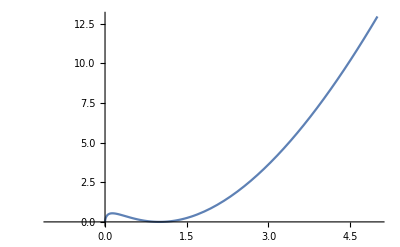

```mathematica
p1=Plot[f[x],{x,-1,5}]
```

```mathematica
ClearAll
```

ClearAll